# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

```mathematica
rbarStar = rbarofrOutside[RStar];
```

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2;
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

## Mass and Density functions from 2405.08113

### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
(*massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}]; Set equal to 1*)
```

```mathematica
rhoCentre[R_] := 63/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar];
```

### Mass function

```mathematica
MassFunc[r_] := 252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3))
```

### Density function

```mathematica
rho[r_] :=rho0(1 - r/RStar)^6
```

## Numerically integrating for the pressure and the phi in α = exp(phi)

### Defining the ODEs

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rho[r] + Pressure)((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

#### Numerically integrating these coupled ODEs

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin},
WorkingPrecision->40
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;

(*Plot[Derivative[1][PhiMetric][r], {r, 0, RStar}]*)
(*Causing the issue it seems, but we have this Analytically!*)
```

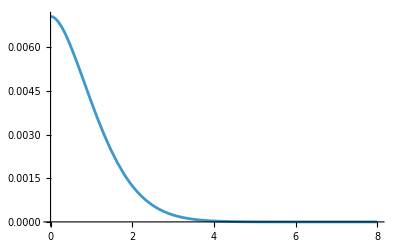

```mathematica
Plot[Pressure[r], {r, 0, RStar}, PlotRange->All]
```

## Solving for r̄(r) and r(r̄) inside

### Defining the ODE

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

### Numerically Integrating the above equation

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin},
WorkingPrecision->40
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

#### Some sanity checks

```mathematica
rbarofrInside[RStar]
rbarofrOutside[RStar] //N
```

6.96410161513775458705489268301174473389

6.9641

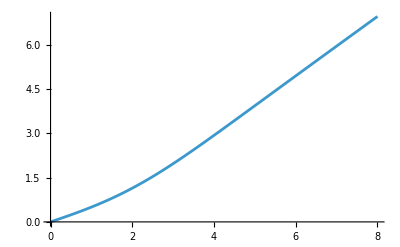

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

### Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Table[ expression, {variable, start, end, step}*)
data = Prepend[Table[
{rbarofrInside[r], r}, 
{r, rmin, RStar, (RStar - rmin)/10000} (*10000 points and A is not messy*)
], {0,0}];
```

```mathematica
rofrbarInside = Interpolation[data];
```

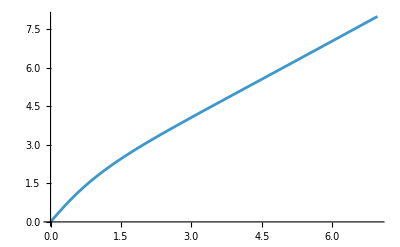

```mathematica
Plot[rofrbarInside[rbar], {rbar, 0, rbarStar}]
```

## Finding the interior metric functions

### Getting αInside(r̄):

```mathematica
αInside[rbar_?NumericQ] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

#### Sanity checks

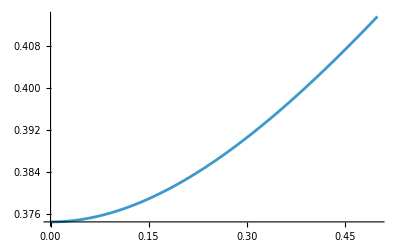

```mathematica
Plot[αInside[rbar], {rbar, 0, .5}]
```

```mathematica
αInside[rbarStar]
α[rbarStar]
```

0.8660254037844386467637231707529361834714

(1-1/(7+4 √3))/(1+1/(7+4 √3))

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
(*αFull[rbar_]:=If[rbar<rbarStar,αInside[rbar],α[rbar]]*)
```

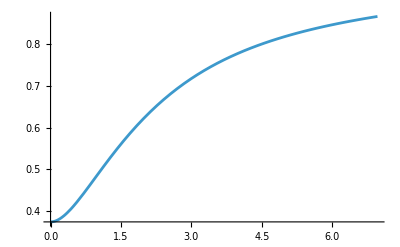

```mathematica
Plot[αFull[rbar], {rbar, 0, rbarStar}]
```

### Making the derivative of alpha continuous

#### Interior derivative in terms of r

Doing things in r first as this is more analytic

```mathematica
dPhidrMetric[r_] := ((MassFunc[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFunc[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r] (*Analytic times numerical integral*)
```

Exterior derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2M)/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r] (*Chain rule*)
```

### Checking to see if it worked

#### Numbers at star boundary

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar] //N
```

0.0180422

0.0180422

```mathematica
diff = Abs[1 - DERalphaIns[rbarofrInside[RStar]]/DERalpha[rbarofrOutside[RStar]]]
```

0.0000209410874772027668220694776039

```mathematica
Abs[Log10[diff]] (*Amount of digits in agreement*)
```

4.6790007690236911686967720663351

#### Plots at star boundary

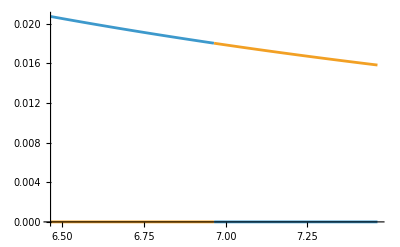

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

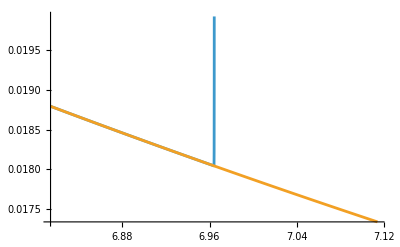

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

### Proper definitions in isotropic coords now

```mathematica
DERαOutside[rbar_] := Module[{r = rofrbarOutside[rbar]}, drbardr[r]  DERαOutsiderbar[r]]

DERαInside[rbar_] := Module[{r = rofrbarInside[rbar]},
dPhidrMetric[r] alpha[r]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

```mathematica
DERαInside[rbarStar]
```

0.01804219591217580514091089939068617

```mathematica
DERαOutside[rbarStar];
```

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

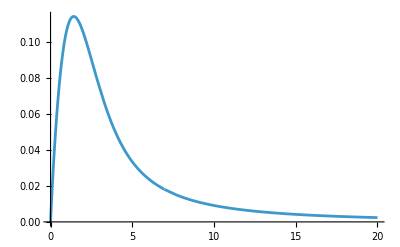

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

Going to do the same derivative setup as the α component for the A component

```mathematica
AInside[rbar_?NumericQ] := rofrbarInside[rbar]/rbar;
```

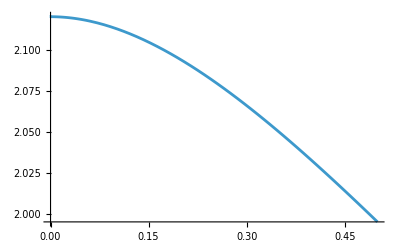

```mathematica
Plot[AInside[rbar], {rbar, 0, .5}]
```

```mathematica
A[rbarStar]
AInside[rbarStar]
```

(1+1/(7+4 √3))^2

1.14874831559185321424343414362416851566

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
(*AFull[rbar_]:=If[rbar<rbarStar,AInside[rbar],A[rbar]]*)
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFunc[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
(*DERAFull[rbar_]:=If[rbar<rbarStar,DERAInside[rbar],DERAOutside[rbar]]*)
```

```mathematica
DERAOutside[rbarStar]
DERAInside[rbarStar]
```

-(4 (1+1/(7+4 √3)))/(7+4 √3)^2

-0.022099489674330444219434004362804943

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar];
```

```mathematica
rho[rbar_] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar < rbarStar},
{0, rbar >= rbarStar}
}
];
```

```mathematica
(*Maybe issue with NDSolve is that there are two numerically integrated things here being used and its causing issues?*)
(*Going to make the above as one interpolating function*)
data = Table[{rbarofrInside[r], Pressure[r]},
{r, rmin, RStar, RStar/1000}];
```

```mathematica
IsotropicCoordsPressure = Interpolation[data];
```

```mathematica
(*Solved the issue of the solver not being able to get an equation for rbar'[t] (method residual error)*)
```

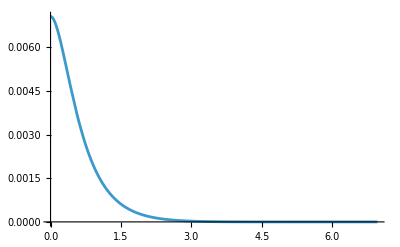

```mathematica
Plot[IsotropicCoordsPressure[rbar], {rbar, 0, rbarStar}, PlotRange->All]
```

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6
rhodummy'[r];
drhodr[r_] := (-6 rho0)/RStar(1-r/RStar)^5
```

#### Speed of sound in isotropic coordinates

```mathematica
cutoffIso = .97rbarStar
```

6.75518

```mathematica
asosEndInterp[rbar_] := Module[{r=rofrbarInside[rbar]},Sqrt[dPdr[r,Pressure[r]]/drhodr[r]]
]
```

```mathematica
asosEndInterp[.9987rbarStar]
```

0.0000259352

```mathematica
data = Prepend[Table[
{rbar, asosEndInterp[rbar]}, 
{rbar, cutoffIso, .999rbarStar, (rbarStar - cutoffIso)/10} (*10000 points and A is not messy*)
], {rbarStar, asosEndInterp[.9987rbarStar]}];
```

```mathematica
asosEnd = Interpolation[data]
```

InterpolatingFunction[…]

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<cutoffIso},{asosEnd[rbar],cutoffIso<=rbar<=rbarStar},
{asosEnd[rbarStar], rbar > rbarStar}
}
]
]
```

InterpolatingFunction::dmval: Input value {6.70518} lies outside the range of data in the interpolating function. Extrapolation will be used.

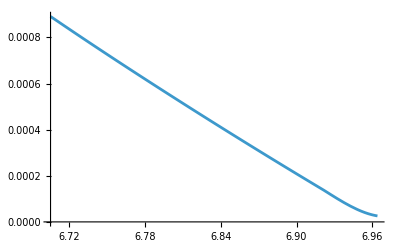

```mathematica
Plot[asosEnd[rbar], {rbar, cutoffIso-0.05, rbarStar}]
```

## Setting up 2D ODEs for new density profile:

Constants that are going to be used

```mathematica
m = 10^-6;
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.98;
x2=1.02;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.98},
{anaylticline[Μach], 0.98 < Μach  < 1.02},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.02}
}];
```

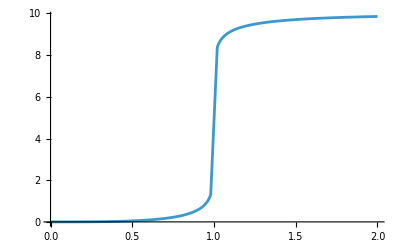

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, PlotRange->All, Exclusions->None]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] :=((√(ur^2+(uphi/rbar)^2))/AInside[rbar])/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
mdot[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (4Pi rho[rbar] m^2)/((asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -((4 Pi αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))ur;

dpdtaccretionphi[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -((4 Pi αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))uphi
```

Drag

```mathematica
dpdtdragphi[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (-4π αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := 252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3));
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
(*eccentricity = 9/11; (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)*)
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];

rperiapsis[eccentricity, ptilde];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[m, rbarStar,0, AngularMomentumUphi0]
duphidtInside[m, rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

InterpolatingFunction::dmval: Input value {1/2 (7+4 √3)} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00219943

-5.4786×10^-9 η

0.0466817

```mathematica
t0=0;
tEnd=10000;
η = 1.5 10^4;

Monitor[
solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->30,

StepMonitor:>(currentTime = t)(*Machine precision and 20k max steps also works*)
][[1]],
Column[{
Row[{"Progress: ", ProgressIndicator[currentTime, {t0, tEnd}]}],
Row[{"Current Time: ", NumberForm[currentTime, {6, 2}], " / ",  tEnd}] (*Amount of digits displayed, amount of decimals rounded*)
}]
];
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {6.96410161513775458705489268301} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.96410161513775458705451162236} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.96410129791025296122312736011} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Abs[6.9641016151377545870545116223626341032952432073615913327815 - rbarStar]*10000000000 (*Error is miniscule now on every entry :)))))))))*)
```

3.8106064911063059036730025916992333×10^-12

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

4971.76651811085396177402174743

159.739

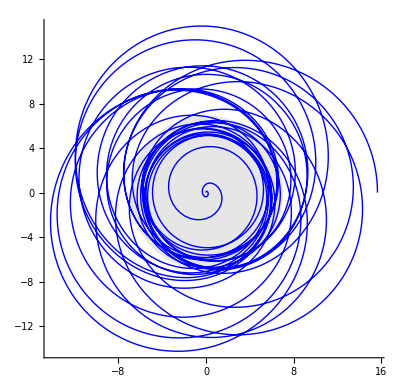

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
FRRrFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRr[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRrIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

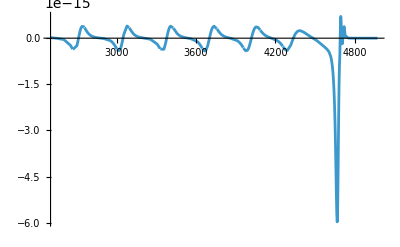

```mathematica
Plot[FRRrFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 2500, tFinish}, PlotRange->All]
```

```mathematica
FRRphiFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRphi[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRphiIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

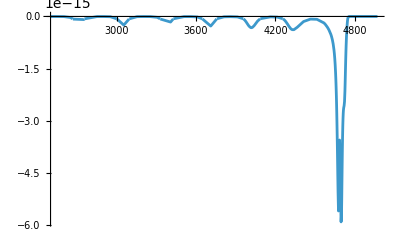

```mathematica
Plot[FRRphiFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 2500, tFinish}, PlotRange->All]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

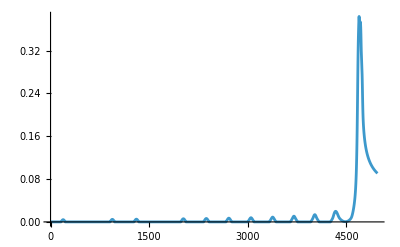

```mathematica
Plot[asosPiecewise[rbarNumIn[t]],{t,0,tFinish}, PlotRange->All]
```

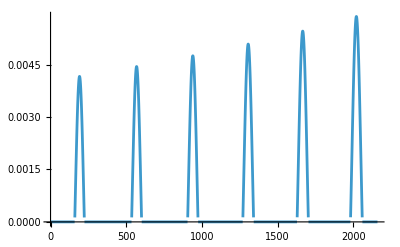

```mathematica
Plot[
{
Piecewise[
{
{0,rbarNumIn[t]>=rbarStar},
{asosPiecewise[rbarNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

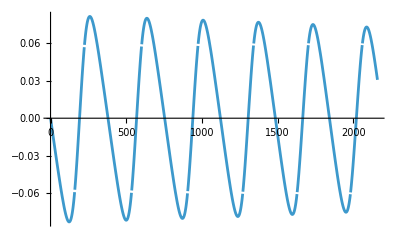

```mathematica
Plot[
{
Piecewise[
{
{drBardt[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{drBardtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

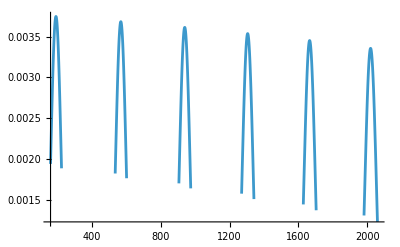

```mathematica
Plot[
{
Piecewise[
{
{durdt2DOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{durdt2DInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

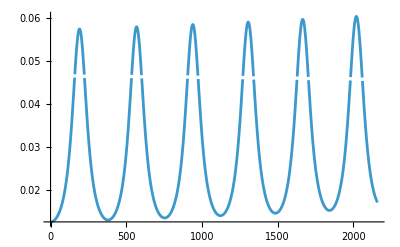

```mathematica
Plot[
{
Piecewise[
{
{dphidtOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{dphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

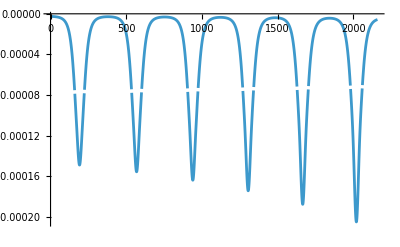

```mathematica
Plot[
{
Piecewise[
{
{duphidtOutside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]], rbarNumIn[t]>=rbarStar},
{duphidtInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

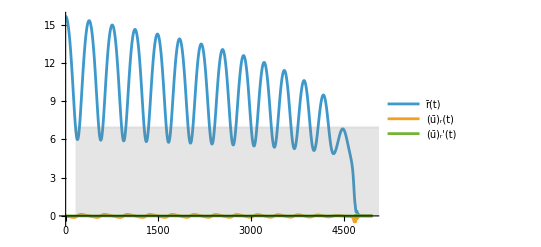

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

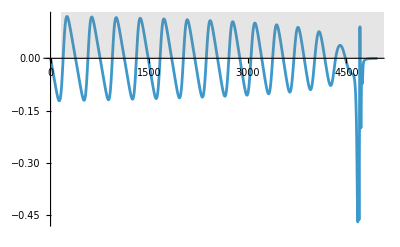

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

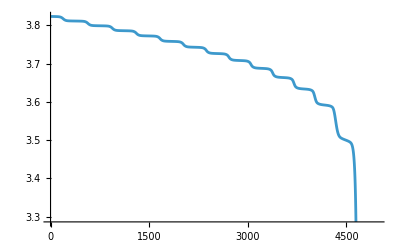

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

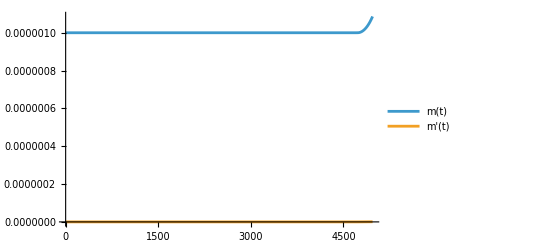

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

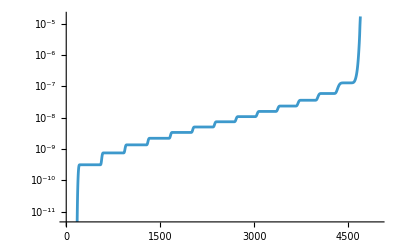

```mathematica
LogPlot[Abs[1 - massNumIn[t]/massNumIn[0]], {t, 0, tFinish}]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

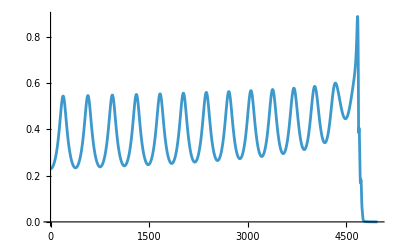

```mathematica
Plot[umag[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None] (*Normal behaviour judging from rho=const simulation*)
```

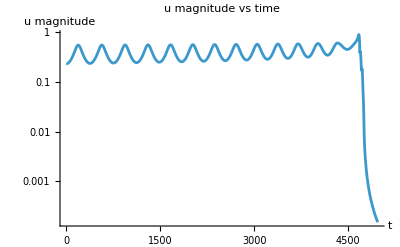

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
(*Show me the value of u at tfinish*)
umag[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn
```

0.00015075546842777349929151

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

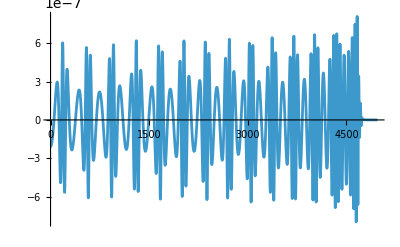

```mathematica
Plot[hplusFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

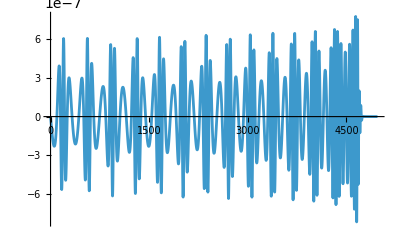

```mathematica
Plot[hxFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

## Energy loss during orbits CHECK angles and other assumptions made by authors for these formulae especially the angular momentum stuff.

### Instantaneous energy loss (coordinate system dependent)

```mathematica
dEdtInside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarInside[rbar],rd,phid},rd=drBardtInside[rbar,ur,uphi];
phid=dphidtInside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(MassFunction[r]^2*(8 rd^2+6 (r phid)^2)+r MassFunction[r]*(6 rd^4-6 (3(r phid)^4+(r phid)^2 Mp[r])+rd^2 (63 (r phid)^2+Mp[r]-3 r Mpp[r]))+r^2*(6 (r phid)^4 Mp[r]-rd^2 ((Mp[r])^2+3 (r phid)^2 (13 Mp[r]-3 r Mpp[r]))-rd^4 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))]
```

```mathematica
dEdtOutside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarOutside[rbar],rd,phid},rd=drBardt[rbar,ur,uphi];
phid=dphidtOutside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(M^2*(8 rd^2+6 (r phid)^2)+r M*(6 rd^4-6 (3(r phid)^4)+rd^2 (63 (r phid)^2)))]
```

```mathematica
dEdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dEdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dEdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

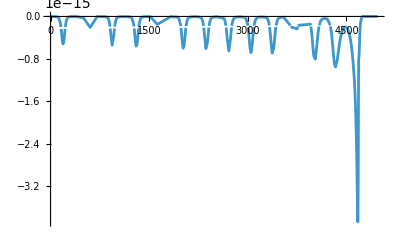

```mathematica
Plot[dEdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

### Average, physical energy loss per orbit

```mathematica
dEdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^3)/(5 a^5 (1-e^2)^(7/2))*(1+(73/24) e^2+(37/96) e^4)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t)

## Angular momentum loss during orbits

### Instantaneous angular momentum loss (coordinate system dependent)

```mathematica
dLdt[m_,M_,a_,e_, phi_]:= -(4(m^2 M^(5/2)))/(5(a^(7/2)(1-e^2)^(7/2)))(1 + e Cos[phi])^3 (8 - 3 e^2 + 20e Cos[phi] + 15 e^2 Cos[2phi])
```

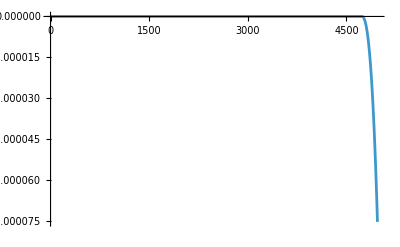

```mathematica
Plot[dLdt[massNumIn[t], M,  rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

### Average, physical angular momentum loss per orbit

```mathematica
(*Formula might need to be adjusted for me as they use the angle phi = 0 for when it crosses the star surface which is not true for me*)
```

```mathematica
dLdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^(5/2))/(5 a^(7/2) (1-e^2)^(2))*(1+(7/8) e^2)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t).

Use E and L to find a(t) and e(t)??